```mathematica
Needs["NDSolve`FEM`"]
MR2=Rectangle[{-2,-2},{2,2}];
MR3=Disk[{0,0},0.1];
```

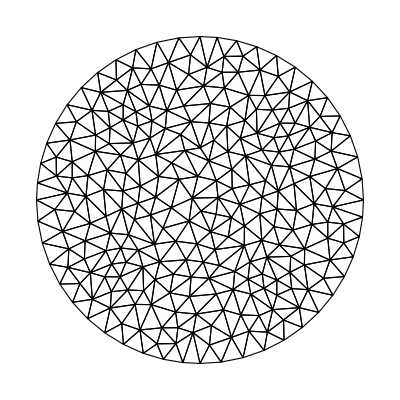

```mathematica
mesh=ToElementMesh[MR3,"MeshElementType"-> TriangleElement,"MeshOrder"->1,MaxCellMeasure->0.0001];
mesh["Wireframe"]
```

```mathematica
np=Dimensions[mesh["Coordinates"]][[1]]
ne=Dimensions[mesh["MeshElements"][[1,1]]][[1]]
```

268

486

```mathematica
SetDirectory[NotebookDirectory[]];
stmp=OpenWrite["../mesh_file/node.dat"];
Write[stmp,np];
For[i=1,i≤np,i++,
out1=ToString[NumberForm[mesh["Coordinates"][[i,1]],20,ExponentFunction->(Null&)]];
out2=ToString[NumberForm[mesh["Coordinates"][[i,2]],20,ExponentFunction->(Null&)]];
out3=out1<>" "<>out2<>"\n";
WriteString[stmp,out3]
]
Close[stmp];
stmp2=OpenWrite["../mesh_file/elm.dat"];
Write[stmp2,ne];
For[i=1,i≤ne,i++,
out1=ToString[mesh["MeshElements"][[1,1,i,1]]];
out2=ToString[mesh["MeshElements"][[1,1,i,2]]];
out3=ToString[mesh["MeshElements"][[1,1,i,3]]];
out4=out1<>" "<>out2<>" "<>out3<>"\n";
WriteString[stmp2,out4]
]
Close[stmp2];
```